# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Solutions 02

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1

Complete the following rate computations:

Take the yield curve {y_1,y_3,y_5} shown below and bootstrap the annual spot rates {s_1,s_2,…,s_5}.  Use interpolation to estimate the missing yields you need to compute the spot curve.

```mathematica
mnYieldCurve={
{1,0.0249},
{3,0.0273},
{5,0.0281}
}
```

{{1,0.0249},{3,0.0273},{5,0.0281}}

Using the spot rate curve, compute the short rates {r_1,r_2,…,r_5}.

Compute the forward rate f_(2,5).

### Solution

#### Yield Curve

```mathematica
xYieldSpline=Interpolation[mnYieldCurve,Method->"Spline",InterpolationOrder->2]
```

InterpolatingFunction[…]

```mathematica
TableForm[Table[{i,xYieldSpline[i]},{i,1,5}],TableHeadings->{None,{"Years","Yield"}}]
```

Years | Yield
1 | 0.0249
2 | 0.0263
3 | 0.0273
4 | 0.0279
5 | 0.0281

#### Spot Curve

s_1=y_1
s_i=((c^(i)+F^(i))/(S^(i)-∑_(j=1)^(i-1) c^(i)/(1+s_j)^j))^(1/i)-1

Under the assumption that the securities are trading at par, we can assume without loss of generality that prices and face amounts are $1. This would make the coupon amount y_i for an i-period bond. Thus, the initial condition and bootstrap simplifies to:

s_1=y_1

s_i=((y_i+1)/(1-∑_(j=1)^(i-1) y_i/(1+s_j)^j))^(1/i)-1

We can use a For[ ] loop to compute the spot curve.

```mathematica
?For
```

The initial condition sets up a spot curve with one rate:

```mathematica
mnSpotCurve={{1,xYieldSpline[1]}}
```

{{1,0.0249}}

We can then simply translate the bootstrap to:

```mathematica
For[i=2,i≤5,i++,
mnSpotCurve=Append[
mnSpotCurve,
{
i,
((1+xYieldSpline[i])/(1-Sum[xYieldSpline[i]/(1+mnSpotCurve⟦j,2⟧)^j,{j,1,i-1}]))^(1/i)-1
}
]
]
```

```mathematica
mnSpotCurve
```

{{1,0.0249},{2,0.0263184},{3,0.0273404},{4,0.0279566},{5,0.0281572}}

```mathematica
TableForm[Table[{i,xYieldSpline[i],mnSpotCurve⟦i,2⟧},{i,1,5}],TableHeadings->{None,{"Years","Yield","Spot"}}]
```

Years | Yield | Spot
1 | 0.0249 | 0.0249
2 | 0.0263 | 0.0263184
3 | 0.0273 | 0.0273404
4 | 0.0279 | 0.0279566
5 | 0.0281 | 0.0281572

#### Short Rates

(1+s_i)^i=(1+r_1)(1+r_2) … (1+r_(i-1))(1+r_i)

The obvious initial condition and bootstrap are:

1+s_1=1+r_1
(1+s_i)^i=(1+s_(i-1))^(i-1)(1+r_i)  ⟹  r_i=(1+s_i)^i/(1+s_(i-1))^(i-1)-1

Although we can calculate the short rates via a loop, it is far more efficient to calculate them in one step as vectors. Look up the functions Prepend[ ], Rest[ ], and Most[ ] in the documentation.

```mathematica
mnShortRates=Transpose[{
Range[1,5],
Prepend[(Rest[#]/Most[#]-1)&[(1+mnSpotCurve⟦All,2⟧)^Range[5]],mnSpotCurve⟦1,2⟧]
}]
```

{{1,0.0249},{2,0.0277388},{3,0.0293873},{4,0.0298076},{5,0.0289601}}

```mathematica
TableForm[Table[{i,xYieldSpline[i],mnSpotCurve⟦i,2⟧,mnShortRates⟦i,2⟧},{i,1,5}],TableHeadings->{None,{"Years","Yield","Spot","Short"}}]
```

Years | Yield | Spot | Short
1 | 0.0249 | 0.0249 | 0.0249
2 | 0.0263 | 0.0263184 | 0.0277388
3 | 0.0273 | 0.0273404 | 0.0293873
4 | 0.0279 | 0.0279566 | 0.0298076
5 | 0.0281 | 0.0281572 | 0.0289601

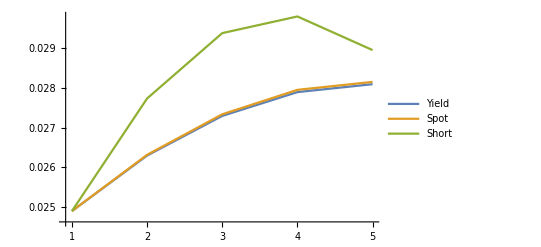

```mathematica
ListLinePlot[{Table[{i,xYieldSpline[i]},{i,1,5}],mnSpotCurve,mnShortRates},PlotLegends->{"Yield","Spot","Short"}]
```

We can check to see if we can recover the spot rates from the short rates by:

s_i=((1+r_1)(1+r_2) … (1+r_(i-1))(1+r_i))^(1/i)-1

You should verify why the above makes sense.

```mathematica
mnSpotCurve⟦All,2⟧-(Rest[FoldList[Times,1,(1+mnShortRates⟦All,2⟧)]]^(1/Range[5])-1)
```

{7.63278×10^-17,0.,0.,0.,0.}

Also, note from the plot of the short rates above that as we get farther and farther from the original yield curve the computations seem to become less rough. This possible numerical instability is also something that a “real world” computation may need to deal with.

#### Forward Rate f_(2,5)

f_(i, j)=((1+s_j)^j/(1+s_i)^i)^(1/(j-i))-1

```mathematica
nForward2to5=((1+mnSpotCurve⟦5,2⟧)^5/(1+mnSpotCurve⟦2,2⟧)^2)^(1/(5-2))-1
```

0.0293849

## Question 2

We are dealing with several projects whose benefits (i.e., their PVs) are represented by a vector b and costs by a vector c. Given the total available capital k, we have the basic zero-one programming problem:

max_x { b^T x | c^T x ≤ k, x_i ϵ  {0, 1}}

There are 10 separate projects, so x={x_1,x_2,…,x_9,x_10}.

However, you find that there are certain interdependencies that are not properly represented in the above integer linear program.

Project 1 cannot be done, unless at least one of project 4 and project 7 are done.

Project 2 cannot be done unless both project 5 and project 8 are done.

Project 3 and project 9 cannot both be done, but neither or exactly one of them may be done.

Define the additional constraints necessary to achieve the conditions above.

### Solution

The key insight is that the constraints below work in the context that we have constrained x_i∈{0,1}.

#### Project 1 cannot be done, unless at least one of project 4 and project 7 are done.

This constraint ensures that x_1 cannot be 1 unless at least one of x_4 or x_7 are 1. It is also acceptable that both x_4 and x_7 are 1.

x_1≤x_4+x_7

#### Project 2 cannot be done unless both project 5 and project 8 are done.

This pair of constraints mean that x_2 cannot be 1 unless both x_5 and x_8 are 1.

x_2≤x_5
x_2≤x_8

#### Project 3 and project 9 cannot both be done, but neither or exactly one of them may be done.

This constraint allows both x_3 and x_9 to be 0 but only one of them to be 1.

x_3+x_9≤1

## Question 3

Use FinancialBond[ ] to compute the following:

A newly issued $10,000 bond with a ten-year term has a 4% coupon rate and pays semi-annually. The current market yield for a ten-year bond of this type is 3.7%. What is the current market price of the bond?

A $10,000 bond with a five-year term, a 3.7% coupon rate paying semi-annually was issued eight months ago. The current market yield is 3.5%.

What is the current price of the bond?

What is the accrued interest on the bond?

Consider a $10,000 semi-annual bond with a twenty-year term and a 4.5% coupon rate. The bond was issued five-years ago and currently trades at a price of $10,500. What is the yield on the bond?

### Solution

A newly issued $10,000 bond with a ten-year term has a 4% coupon rate and pays semi-annually. The current market yield for a ten-year bond of this type is 3.7%. What is the current market price of the bond?

```mathematica
FinancialBond[{"Coupon"->0.04,"FaceValue"->10000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->0.037,"Settlement"->0}]
```

10248.9

A $10,000 bond with a five-year term, a 3.7% coupon rate paying semi-annually was issued eight months ago. The current market yield is 3.5%.

What is the current price of the bond?

What is the accrued interest on the bond?

```mathematica
FinancialBond[{"Coupon"->0.037,"FaceValue"->10000,"Maturity"->5,"CouponInterval"->1/2},{"InterestRate"->0.035,"Settlement"->8/12},{"Value","AccruedInterest"}]
```

{10079.4,61.6667}

Consider a $10,000 semi-annual bond with a twenty-year term and a 4.5% coupon rate. The bond was issued five-years ago and currently trades at a price of $10,500. What is the yield on the bond?

```mathematica
FindRoot[10500.==FinancialBond[{"Coupon"->0.045,"FaceValue"->10000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->y,"Settlement"->5}],{y,0.045}]
```

{y→0.0340402}

## Question 4

The TUV corporation has just paid a dividend and its next dividend is estimated to be $1.4 million. It has a total market capitalization of $35,000,000. The growth rate for this type of company is 10%. What is the implied discount rate for the dividends of this stock?

### Solution

Solving the dividend discount model for r

S=D_1/(r-g) ⟹ r=(D_1+S g)/S

```mathematica
nDiscountRate=(1.4 10^6+3.5 10^7 0.1)/(35 10^6)
```

0.14

Checking the computation

```mathematica
(1.4 10^6)/(nDiscountRate-0.1)
```

3.5×10^7